```mathematica
SetDirectory["D:\\Физика-матем\\Всеукры 2007-17\\2017 Кривой Рог"]
```

D:\Физика-матем\Всеукры 2007-17\2017 Кривой Рог

```mathematica
im1=Import["heat.txt","Data"]
```

{{26,0},{27,150},{28,360},{29,590},{30,810},{31,1150},{32,1620}}

```mathematica
Transpose[{Transpose[im1][[2]]/1000.,Transpose[im1][[1]]-26.}]
```

{{0.,0.},{0.15,1.},{0.36,2.},{0.59,3.},{0.81,4.},{1.15,5.},{1.62,6.}}

```mathematica
FindFit[%5,T0(1-ⅇ^(-t/τ)),{T0,τ},t]
```

{T0→8.44504,τ→1.29598}

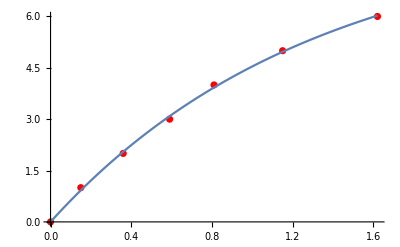

```mathematica
Show[ListPlot[%5,PlotStyle->Red],Plot[T0 (1-ⅇ^(-t/τ))/.{T0->8.445040590867139,τ->1.2959802315431437},{t,0.,1.62}]]
```

```mathematica
im3=Import["cool.txt","Data"]
```

{{32.5,0},{32,60},{31.5,90},{31,160},{30.5,300},{30,420},{29.5,510},{29,600},{28.5,740},{28,810},{27.5,1020},{27,1240},{26.5,1380},{26,1590}}

```mathematica
Transpose[{Transpose[im2][[2]]/1000.,Transpose[im2][[1]]}]
```

{{0.,32.5},{0.06,32},{0.09,31.5},{0.16,31},{0.3,30.5},{0.42,30},{0.51,29.5},{0.6,29},{0.74,28.5},{0.81,28},{1.02,27.5},{1.24,27},{1.38,26.5},{1.59,26}}

```mathematica
FindFit[%16,T0+(32.5-T0) ⅇ^(-t/τ),{T0,τ},t]
```

{T0→24.1586,τ→1.09708}

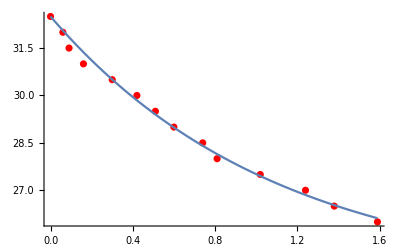

```mathematica
Show[ListPlot[%16,PlotStyle->Red],Plot[T0+(32.5-T0) ⅇ^(-t/τ)/.{T0->24.15861909073897,τ->1.0970847855269437},{t,0.,1.59}]]
```

```mathematica
im3=Import["heat2.txt","Data"]
```

{{25,0},{25.5,60},{26,120},{26.5,210},{27,250},{27.5,360},{28,440},{28.5,540},{29,600},{29.5,720},{30,810},{30.5,960},{31,1080},{31.5,1260},{32,1440},{32.5,1860}}

```mathematica
Transpose[{Transpose[im3][[2]]/1000.,Transpose[im3][[1]]-25.}]
```

{{0.,0.},{0.06,0.5},{0.12,1.},{0.21,1.5},{0.25,2.},{0.36,2.5},{0.44,3.},{0.54,3.5},{0.6,4.},{0.72,4.5},{0.81,5.},{0.96,5.5},{1.08,6.},{1.26,6.5},{1.44,7.},{1.86,7.5}}

```mathematica
FindFit[%31,T0(1-ⅇ^(-t/τ)),{T0,τ},t]
```

{T0→9.45936,τ→1.1086}

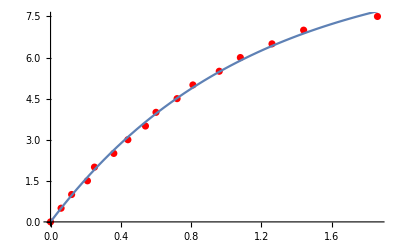

```mathematica
Show[ListPlot[%31,PlotStyle->Red],Plot[T0 (1-ⅇ^(-t/τ))/.{T0->9.459356486413023,τ->1.1086030383417058},{t,0.,1.86}]]
```

```mathematica
0.81-0.67
```

0.14

```mathematica
%/0.81
```

0.17284